(0. | 0.0690066 | 0.06742 | 0.065938 | 0.0645497 | 0.0632456 | 0.0620174 | 0.0608581 | 0.0597614 | 0.058722 | 0.057735
0. | 0.0657952 | 0.0644157 | 0.0631194 | 0.0618984 | 0.0607457 | 0.059655 | 0.058621 | 0.057639 | 0.0567048 | 0.0558146
0. | 0.0627456 | 0.0615457 | 0.0604122 | 0.0593391 | 0.0583212 | 0.0573539 | 0.0564333 | 0.0555556 | 0.0547176 | 0.0539164
0. | 0.0598684 | 0.0588235 | 0.0578315 | 0.056888 | 0.0559893 | 0.0551318 | 0.0543125 | 0.0535288 | 0.052778 | 0.0520579
0. | 0.0571662 | 0.0562544 | 0.0553849 | 0.0545545 | 0.0537603 | 0.0529999 | 0.0522708 | 0.0515711 | 0.0508987 | 0.0502519
0. | 0.0546358 | 0.0538382 | 0.0530745 | 0.0523424 | 0.0516398 | 0.0509647 | 0.0503155 | 0.0496904 | 0.0490881 | 0.0485071
0. | 0.0522708 | 0.0515711 | 0.0508987 | 0.0502519 | 0.0496292 | 0.049029 | 0.0484502 | 0.0478913 | 0.0473514 | 0.0468293
0. | 0.0500626 | 0.0494468 | 0.0488532 | 0.0482805 | 0.0477274 | 0.0471929 | 0.046676 | 0.0461757 | 0.0456912 | 0.0452216
0. | 0.0480015 | 0.0474579 | 0.0469323 | 0.0464238 | 0.0459315 | 0.0454545 | 0.0449921 | 0.0445435 | 0.0441081 | 0.0436852
0. | 0.0460776 | 0.0455961 | 0.0451294 | 0.0446767 | 0.0442374 | 0.0438108 | 0.0433963 | 0.0429934 | 0.0426014 | 0.04222
0. | 0.0442807 | 0.0438529 | 0.0434372 | 0.0430331 | 0.0426401 | 0.0422577 | 0.0418854 | 0.0415227 | 0.0411693 | 0.0408248)

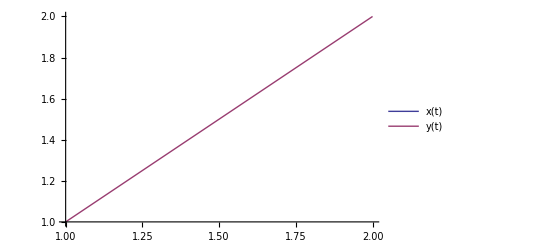

```mathematica
(*Зададим параметр λ*)
λ=1;
(*Зададим отрезок интегрирования*)
a=1;
b=2;
(*Зададим ядро уравнения*)
K[s_,t_]=1/Sqrt[t+s^2];
(*Зададим свободный член уравнения*)
f[t_]=Sqrt[t+1]-Sqrt[t+4]+t;
(*Зададим количество частичных отрезков*)
n=10;
(*Зададим шаг разбиения*)
h=(b-a)/n;
(*Построим разбиение отрезка на частичные*)
T=Table[a+k*h,{k,0,n}];
S=T;
(*Зададим коэффициенты квадратурной формулы*)
(*правых прямоугольников*)
A={0};
A=Join[A,Table[h,{k,1,n}]];
(*Построим сеточную функцию свободного члена уравнения*)
F=Table[f[T[[k]]],{k,1,n+1}];
(*Зададим единичную матрицу порядка n+1*)
IM=IdentityMatrix[n+1];
(*Построим матрицу Фредгольма*)
L=Table[N[A[[k]]*K[S[[j]],T[[k]]]],{j,1,n+1},{k,1,n+1}]//MatrixForm
Fr=IM-λ*L;
(*Найдем каркас приближенного решения уравнения*)
X=Inverse[Fr].F;
(*Выполним интерполяцию найденного приближенного решения*)
TX=Table[{T[[k]],X[[k]]},{k,1,n+1}];
x=Interpolation[TX];
(*Зададим точное решение данного уравнения*)
y[t_]=t;
(*Построим графики точного и приближенного решения в одной системе координат*)
G=Plot[{x[t],y[t]},{t,a,b},PlotLegends->"Expressions"]
```